# Alcubierre warp drive single particle trajectory

## Geometric Quantities

```mathematica
ClearAll[coordsU];
coordsU={t,x,y,z};

ClearAll[vU];
vU={vx[t,x,y,z],vy[t,x,y,z],vz[t,x,y,z]};

ClearAll[gUU];
gUU=α[t,x,y,z]^(-2){
{-1,-vU[[1]],-vU[[2]],-vU[[3]]},
{-vU[[1]],α[t,x,y,z]^2-vU[[1]]vU[[1]],-vU[[1]]vU[[2]],-vU[[1]]vU[[3]]},
{-vU[[2]],-vU[[2]]vU[[1]],α[t,x,y,z]^2-vU[[2]]vU[[2]],-vU[[2]]vU[[3]]},
{-vU[[3]],-vU[[3]]vU[[1]],-vU[[3]]vU[[2]],α[t,x,y,z]^2-vU[[3]]vU[[3]]}
}//FullSimplify;

gLL=FullSimplify[Inverse[gUU]];

ClearAll[nU,nL];
nU=Join[{1/α[t,x,y,z]},vU/α[t,x,y,z]];
nL=FullSimplify[Table[Sum[gLL[[a,b]]nU[[b]],{b,1,4}],{a,1,4}]];
```

## Particle Hamiltonian

```mathematica
ClearAll[pL];
pL={pt,px,py,pz};

ClearAll[H];
H=FullSimplify[1/2Sum[gUU[[a,b]]pL[[a]]pL[[b]],{a,1,4},{b,1,4}]];

ClearAll[dHdpL];
dHdpL=FullSimplify[Table[D[H,pL[[i]]],{i,1,4}]];

ClearAll[dHdqU];
dHdqU=FullSimplify[Table[D[H,coordsU[[i]]],{i,1,4}]];

ClearAll[λRules,Hλ,dqUdλ,dpLdλ];
λRules={pt->pt[λ],px->px[λ],py->py[λ],pz->pz[λ],t->t[λ],x->x[λ],y->y[λ],z->z[λ]};
Hλ=FullSimplify[H/.λRules];
dqUdλ=FullSimplify[dHdpL/.λRules];
dpLdλ=FullSimplify[-dHdqU/.λRules];

ClearAll[stateVector];
stateVector=MapThread[
Equal[#1,#2]&,
{{t'[λ],x'[λ],y'[λ],z'[λ],pt'[λ],px'[λ],py'[λ],pz'[λ]},Join[dqUdλ,dpLdλ]}
];
```

## Hamilton’s equations integration

```mathematica
(* Metric data *)
ClearAll[vx,vy,vz,α];
ClearAll[r,f,v,σ,R];
v=1/2;
σ=2;
R=2;

r[t_,x_,y_,z_]:=Sqrt[(x-v*t)^2+y^2+z^2+10^(-12)];
f[rr_]:=(Tanh[σ(rr+R)]-Tanh[σ(rr-R)])/(2Tanh[σ*R]);

vx[t_,x_,y_,z_]=v*f[r[t,x,y,z]];
vy[t_,x_,y_,z_]=9/10*y/Sqrt[y^2+z^2+10^(-12)]f[r[t,x,y,z]];
vz[t_,x_,y_,z_]=0;
α[t_,x_,y_,z_]=1;

(* Initial data *)
ClearAll[δ,px0,py0,pz0,t0,x0,y0,z0];
δ=-1;

px0=0;
py0=0;
pz0=0;

t0=0;
x0=4;
y0=1;
z0=0;

ClearAll[pt0];
pt0=pt//.Solve[Sum[gUU[[a,b]]{pt,px0,py0,pz0}[[a]]{pt,px0,py0,pz0}[[b]],{a,1,4},{b,1,4}]==-1,pt][[1]];


ClearAll[initialData];
initialData={t[0]==t0,x[0]==x0,y[0]==y0,z[0]==z0,pt[0]==pt0,px[0]==px0,py[0]==py0,pz[0]==pz0};

ClearAll[equations,variables];
equations=Join[stateVector,initialData];
variables={t,x,y,z,pt,px,py,pz};


(* System integration *)
ClearAll[λmin,λmax];
λmin=0;
λmax=200;

ClearAll[sol];
sol=Flatten[
NDSolve[
equations,
variables,
{λ,λmin,λmax},
Method->{
"ImplicitRungeKutta",
"DifferenceOrder"->4
},
PrecisionGoal->MachinePrecision,
AccuracyGoal->MachinePrecision
]
];

ClearAll[equations];
ClearAll[initialData];
ClearAll[pt0];
ClearAll[δ,px0,py0,pz0,t0,x0,y0,z0];
ClearAll[r,f,v,σ,R];
ClearAll[vx,vy,vz,α];
```

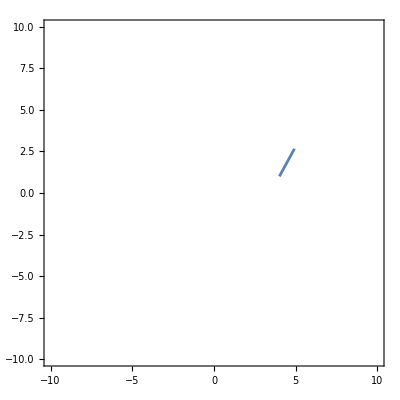

```mathematica
ParametricPlot[
{x[λ],y[λ]}//.sol,{λ,λmin,λmax},
Axes->False,
Frame->True,
AspectRatio->1,
PlotRange->{{-10,10},{-10,10}}
]
```